```mathematica
xData=Flatten[Import["/Users/nevencaplar/Documents/Variability/Github/Variability/HSC/Test/res_redshift_array_single_g.txt","CSV"]];
yData=Flatten[Import["/Users/nevencaplar/Documents/Variability/Github/Variability/HSC/Test/res_delta_redshift_via_redshift_array_single_g.txt","CSV"]];
errData=
Flatten[Import["/Users/nevencaplar/Documents/Variability/Github/Variability/HSC/Test/res_delta_redshift_via_redshift_err_array_single_g","CSV"]];
```

```mathematica
err2Data
data={xData,yData}//Transpose;
```

{0.0438316471284229403,0.0464692132180498652,0.0490977998611902278,0.0474340958071897412,0.041705446687543099,0.0365554543665351991,0.0440112644750335486,0.0386563183956148901,0.0351154854542720801,0.036411483330621254,0.0334590861103671172,0.040115656136861369,0.0348500904770983541,0.0389514832588646401,0.0403819426711624283,0.0374453933688992519,0.0310559979268847375,0.0393770385154833674,0.0429264828636386556,0.0377102379447091241,0.0343131502747704639,0.0353408562895492981,0.036689867306978062,0.0361967191800537033,0.0449192398578881214,0.0382694648681168106,0.0354940925053986722,0.0395865218003216626,0.0460081468993732423,0.0328321768152447513,0.0458107392307655834,0.0407966610292309975,0.0329454800865381578,0.0414071567292727122,0.0363161407465648553,0.0330963729929585962,0.0331561550315264339,0.0294265180888328773,0.0334209499189830964,0.0283844011159733525,0.0330728602208340411,0.0301498020551253833,0.0371420897051259885,0.0372813998546958694,0.0326482765046143819,0.0301199479924286542,0.0344039278531320589,0.031026161130868677,0.0361834882439343933,0.0330537232170052889,0.0281555074776550854,0.0291808663839940585,0.0311575435182722856,0.0283812427712413669,0.025770297026496386,0.0240878807570423376,0.0277659266484155676,0.0316273742007533235,0.0421689499566460235}

```mathematica
lm=LinearModelFit[data,x,x,VarianceEstimatorFunction->(Mean[#^2]&),Weights->1/errData,ConfidenceLevel->0.667 ]
```

FittedModel[-0.190726897020298269+0.0566080683048194797 x]

```mathematica
lm=LinearModelFit[data,x,x,Weights->1/errData^2,ConfidenceLevel->0.667 ]
```

FittedModel[-0.18600906097720911+0.0535681793529125572 x]

```mathematica
(*https://reference.wolfram.com/language/tutorial/StatisticalModelAnalysis.html
```

```mathematica
lm["MeanPrediction"]
```

FittedModel::notprop: MeanPrediction is not a known property for …. Use …["Properties"] for a list of properties.

FittedModel[-0.18600906097720911+0.0535681793529125572 x][MeanPrediction]

```mathematica
lm["CorrelationMatrix"]
```

{{1.,-0.9050931323146903},{-0.9050931323146903,1.}}

```mathematica
lm["CovarianceMatrix"]
```

{{0.0001228499300135923,-0.00005979558889774918},{-0.00005979558889774918,0.00003495351309171276}}

```mathematica
FullSimplify[1+lm["BasisFunctions"].lm["CovarianceMatrix"].Transpose[{lm["BasisFunctions"]}]]
```

{1.0001228499300135923+(-0.0001195911777954984+0.00003495351309171276 x) x}

```mathematica
{lm["EstimatedVariance"],lm["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]}
```

{1.08795513085446,0.001480385491738388}

```mathematica
lm["MeanPredictionBands"]
```

{-0.18600906097720911+0.0535681793529125572 x-0.976383944458605191 √(0.0001336552116833991-0.0001301098354875404 x+0.00003802785390951743 x^2),-0.18600906097720911+0.0535681793529125572 x+0.976383944458605191 √(0.0001336552116833991-0.0001301098354875404 x+0.00003802785390951743 x^2)}

```mathematica
StudenPredictedResponsetTDistribution[56][0.1667]
```

StudentTDistribution[56][0.1667]

```mathematica
PDF[StudentTDistribution[56],0.25]
```

0.384738

```mathematica
Quantile[StudentTDistribution[97],0.1667]
```

-0.972138

```mathematica
N[Quartiles[StudentTDistribution[56]]]
```

{-0.678896,0.,0.678896}

```mathematica
Dimensions[data]
```

{59,2}

```mathematica
lm["EstimatedVariance"]
```

0.001462893359882242

```mathematica
EstimatedVariance
```

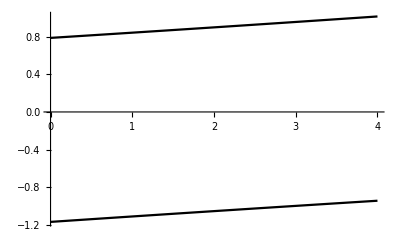

```mathematica
Plot[lm["SinglePredictionBands"],{x,0,4},PlotStyle->Black]
```

```mathematica
lm=LinearModelFit[data,{x},x,VarianceEstimatorFunction->(Mean[#^2]&),Weights->1/errData,ConfidenceLevel->0.667 ]
```

FittedModel[-0.190726897020298269+0.0566080683048194797 x]

```mathematica
lm["MeanPredictionBands"]
```

{-0.190726897020298269+0.0566080683048194797 x-0.976383944458605191 √(4.83649436366502×10^-6-4.849873762462369×10^-6 x+1.484170012709496×10^-6 x^2),-0.190726897020298269+0.0566080683048194797 x+0.976383944458605191 √(4.83649436366502×10^-6-4.849873762462369×10^-6 x+1.484170012709496×10^-6 x^2)}

```mathematica
lm["CovarianceMatrix"]
```

{{4.83649436366502×10^-6,-2.424936881231185×10^-6},{-2.424936881231185×10^-6,1.484170012709496×10^-6}}

```mathematica
FullSimplify[1+lm["BasisFunctions"].lm["CovarianceMatrix"].Transpose[{lm["BasisFunctions"]}]]
```

{1.00000483649436366502+(-4.849873762462369×10^-6+1.484170012709496×10^-6 x) x}

```mathematica
lm["SinglePredictionBands"]
```

{-0.190726897020298269+0.0566080683048194797 x-0.976383944458605191 √(0.001467729854245907-4.849873762462369×10^-6 x+1.484170012709496×10^-6 x^2),-0.190726897020298269+0.0566080683048194797 x+0.976383944458605191 √(0.001467729854245907-4.849873762462369×10^-6 x+1.484170012709496×10^-6 x^2)}

```mathematica
Sqrt[lm["EstimatedVariance"]]
```

0.03824778895416364

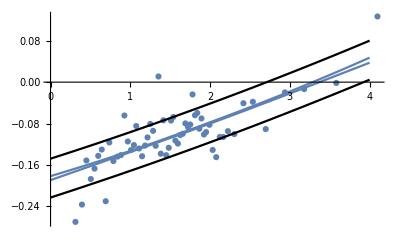

```mathematica
Show[ListPlot[data],Plot[lm["MeanPredictionBands"],{x,0,4}],Plot[lm["SinglePredictionBands"],{x,0,4},PlotStyle->Black]]
```

```mathematica
dataT=data;
dataT[[All,1]]=15/(1+dataT[[All,1]]);
```

```mathematica
xprime=15/(1+x)
```

```mathematica
(1+x)=15/xprime
x=15/xprime-1
```

```mathematica
lm=LinearModelFit[dataT,{xprime,xprime^2,xprime^3},xprime,VarianceEstimatorFunction->(Mean[#^2]&),Weights->1/errData,ConfidenceLevel->0.667,IncludeConstantBasis->False]
```

FittedModel[-0.0100732841778533575 xprime-0.000894512562532918891 («6»)^2+2.54234140934123939×10^-6 xprime^3]

```mathematica
Normal[lm]/.xprime->(15/(1+x))
```

0.0777842754187162161+0.16609785474495839/(1+x)^2-0.500983635641067423/(1+x)

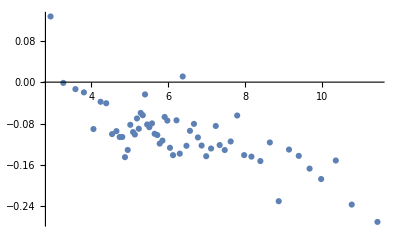

```mathematica
Show[ListPlot[dataT],Plot[Normal[lm],{x,0,4}]]
```

```mathematica
lm["SinglePredictionBands"]/.xprime->(15/(1+x))
```

{0.0455435467671878783-0.348322774010035868/(1+x)-0.976383944458605191 √(0.001559971760205715+0.00006215249625938308/(1+x)^2-0.00005131050642227031/(1+x)),0.0455435467671878783-0.348322774010035868/(1+x)+0.976383944458605191 √(0.001559971760205715+0.00006215249625938308/(1+x)^2-0.00005131050642227031/(1+x))}

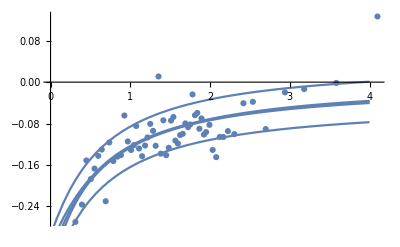

```mathematica
Show[ListPlot[data],Plot[Normal[lm]/.xprime->(15/(1+x)),{x,0,4}],Plot[lm["MeanPredictionBands"]/.xprime->(15/(1+x)),{x,0,4}],Plot[lm["SinglePredictionBands"]/.xprime->(15/(1+x)),{x,0,4}]]
```

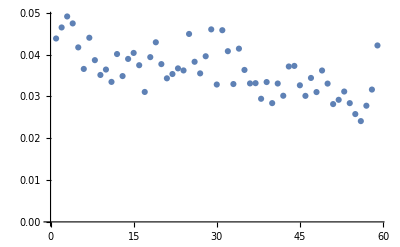

```mathematica
ListPlot[err2Data]
```